```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g-g- t- t (1-loop)

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 47 Particles insertions

```mathematica
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->True,SMP->True,LorentzIndexNames-> {μ,ν},Contract->True,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings//.{GS->gs}),ChangeDimension->D]/.{GS->gs};
nonZero={};
(* Keep only the diagrams up to gs^2 and containing yDM *)
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	M=Normal[Series[M,{gs,0,2}]];
	M=Normal[Series[M,{yDM,0,2}]];
	M=DiracSimplify[M];
    If[!M==={0} && !FreeQ[M,yDM] ,AppendTo[nonZero,n]];
];
```

in total: 47 Particles amplitudes

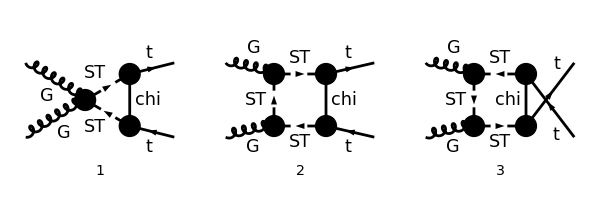

```mathematica
goodDiags=DiagramExtract[allDiags,nonZero];
(* goodDiags=DiagramExtract[goodDiags,{2,3,6,7,8,9}]; *)
goodDiags=DiagramExtract[goodDiags,{4,10,11}];
(* goodDiags=DiagramExtract[goodDiags,{4}]; *)
Paint[goodDiags,ColumnsXRows->{3,1},ImageSize->{ 600,200},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},LorentzIndexNames->{μ,ν},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 3 Particles amplitudes

-gs^2 yDM^2 ((γ·q).(γ̄)^6 ((g^μν ((T^Glu1 T^Glu2)_Col3Col4+(T^Glu2 T^Glu1)_Col3Col4))/((q^2-mChi^2).((p1+q)^2-mST^2).((p2-q)^2-mST^2))+(k2^ν+2 q^ν) (k2^μ-p1^μ-p2^μ+2 q^μ) (((T^Glu1 T^Glu2)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))-((T^Glu2 T^Glu1)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))))+(k2^ν+2 q^ν) (k2^μ-p1^μ-p2^μ+2 q^μ) ((((γ·k2).(γ̄)^6-(γ·p2).(γ̄)^6) (T^Glu1 T^Glu2)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))+(((γ·p1).(γ̄)^6-(γ·k2).(γ̄)^6) (T^Glu2 T^Glu1)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify);
```

```mathematica
ampEsimp=ExpandScalarProduct[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

## On - Shell Case

since we are only interested in q q -> tt or gg -> tt, the t - t - g - g vertex only contributes when all external particles are on - shell, so we make use of this to simplify the final expressions

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,MT,MT,0,0];
```

```mathematica
ampEsimp2=Simplify[DiracSimplify[ampEsimp]]/.{s+t+u-> 2 MT^2};
```

## EFT Limit of Integrals

```mathematica
(* Define global assumptions, valid in the EFT limit *)
$Assumptions={MT>0,mST>mChi,mST>0,mChi>0,mST>MT,mChi>MT,Im[s]==0,Im[t]==0,Im[u]==0,s>4MT^2};
```

```mathematica
loopInts =Cases2[ampEsimp2,PaVe];
```

```mathematica
loopIntsEFT=Table[{loopInts[[i]],FullSimplify[PaXEvaluate[loopInts[[i]]/.{MT-> x MT,s->x^2 MT,t->x^2 t, u ->x^2 u},PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{x,0,0}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi)),x->1}]},{i,1,Length[loopInts]}]
```

(C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) | -(-4 mChi^2 mST^2-4 mChi^4 log(mChi/mST)+3 mChi^4+mST^4)/(64 π^4 (mChi^2-mST^2)^3)
D_1(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -(3 mChi^4 mST^2-6 mChi^2 mST^4-12 mChi^4 mST^2 log(mChi/mST)+2 mChi^6+mST^6)/(192 π^4 mST^2 (mChi^2-mST^2)^4)
D_1(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -(3 mChi^4 mST^2-6 mChi^2 mST^4-12 mChi^4 mST^2 log(mChi/mST)+2 mChi^6+mST^6)/(192 π^4 mST^2 (mChi^2-mST^2)^4)
D_2(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | ((mChi-mST) (mChi+mST) (5 mChi^2+mST^2)-4 (2 mChi^2 mST^2+mChi^4) log(mChi/mST))/(64 π^4 (mChi^2-mST^2)^4)
D_2(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | ((mChi-mST) (mChi+mST) (5 mChi^2+mST^2)-4 (2 mChi^2 mST^2+mChi^4) log(mChi/mST))/(64 π^4 (mChi^2-mST^2)^4)
D_3(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -(3 mChi^4 mST^2-6 mChi^2 mST^4-12 mChi^4 mST^2 log(mChi/mST)+2 mChi^6+mST^6)/(192 π^4 mST^2 (mChi^2-mST^2)^4)
D_3(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -(3 mChi^4 mST^2-6 mChi^2 mST^4-12 mChi^4 mST^2 log(mChi/mST)+2 mChi^6+mST^6)/(192 π^4 mST^2 (mChi^2-mST^2)^4)
D_00(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (-4 mChi^2 mST^2-4 mChi^4 log(mChi/mST)+3 mChi^4+mST^4)/(128 π^4 (mChi^2-mST^2)^3)
D_00(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (-4 mChi^2 mST^2-4 mChi^4 log(mChi/mST)+3 mChi^4+mST^4)/(128 π^4 (mChi^2-mST^2)^3)
D_11(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (-10 mChi^6 mST^2+18 mChi^4 mST^4-6 mChi^2 mST^6+24 mChi^6 mST^2 log(mChi/mST)-3 mChi^8+mST^8)/(576 π^4 mST^2 (mST^2-mChi^2)^5)
D_11(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (-10 mChi^6 mST^2+18 mChi^4 mST^4-6 mChi^2 mST^6+24 mChi^6 mST^2 log(mChi/mST)-3 mChi^8+mST^8)/(576 π^4 mST^2 (mST^2-mChi^2)^5)
D_12(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (9 mChi^4 mST^2+9 mChi^2 mST^4+12 (3 mChi^4 mST^2+mChi^6) log(mChi/mST)-17 mChi^6-mST^6)/(576 π^4 (mChi^2-mST^2)^5)
D_12(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (9 mChi^4 mST^2+9 mChi^2 mST^4+12 (3 mChi^4 mST^2+mChi^6) log(mChi/mST)-17 mChi^6-mST^6)/(576 π^4 (mChi^2-mST^2)^5)
D_13(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (-10 mChi^6 mST^2+18 mChi^4 mST^4-6 mChi^2 mST^6+24 mChi^6 mST^2 log(mChi/mST)-3 mChi^8+mST^8)/(1152 π^4 mST^2 (mST^2-mChi^2)^5)
D_13(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (-10 mChi^6 mST^2+18 mChi^4 mST^4-6 mChi^2 mST^6+24 mChi^6 mST^2 log(mChi/mST)-3 mChi^8+mST^8)/(1152 π^4 mST^2 (mST^2-mChi^2)^5)
D_22(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | ((mChi-mST) (mChi+mST) (10 mChi^2 mST^2+mChi^4+mST^4)-12 mChi^2 mST^2 (mChi^2+mST^2) log(mChi/mST))/(96 π^4 (mChi^2-mST^2)^5)
D_22(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | ((mChi-mST) (mChi+mST) (10 mChi^2 mST^2+mChi^4+mST^4)-12 mChi^2 mST^2 (mChi^2+mST^2) log(mChi/mST))/(96 π^4 (mChi^2-mST^2)^5)
D_23(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (9 mChi^4 mST^2+9 mChi^2 mST^4+12 (3 mChi^4 mST^2+mChi^6) log(mChi/mST)-17 mChi^6-mST^6)/(576 π^4 (mChi^2-mST^2)^5)
D_23(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (9 mChi^4 mST^2+9 mChi^2 mST^4+12 (3 mChi^4 mST^2+mChi^6) log(mChi/mST)-17 mChi^6-mST^6)/(576 π^4 (mChi^2-mST^2)^5)
D_33(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (-10 mChi^6 mST^2+18 mChi^4 mST^4-6 mChi^2 mST^6+24 mChi^6 mST^2 log(mChi/mST)-3 mChi^8+mST^8)/(576 π^4 mST^2 (mST^2-mChi^2)^5)
D_33(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (-10 mChi^6 mST^2+18 mChi^4 mST^4-6 mChi^2 mST^6+24 mChi^6 mST^2 log(mChi/mST)-3 mChi^8+mST^8)/(576 π^4 mST^2 (mST^2-mChi^2)^5)
D_001(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (18 mChi^4 mST^2-9 mChi^2 mST^4+12 mChi^6 log(mChi/mST)-11 mChi^6+2 mST^6)/(1152 π^4 (mChi^2-mST^2)^4)
D_001(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (18 mChi^4 mST^2-9 mChi^2 mST^4+12 mChi^6 log(mChi/mST)-11 mChi^6+2 mST^6)/(1152 π^4 (mChi^2-mST^2)^4)
D_002(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (3 mChi^4 mST^2-6 mChi^2 mST^4-12 mChi^4 mST^2 log(mChi/mST)+2 mChi^6+mST^6)/(384 π^4 (mChi^2-mST^2)^4)
D_002(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (3 mChi^4 mST^2-6 mChi^2 mST^4-12 mChi^4 mST^2 log(mChi/mST)+2 mChi^6+mST^6)/(384 π^4 (mChi^2-mST^2)^4)
D_003(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (18 mChi^4 mST^2-9 mChi^2 mST^4+12 mChi^6 log(mChi/mST)-11 mChi^6+2 mST^6)/(1152 π^4 (mChi^2-mST^2)^4)
D_003(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (18 mChi^4 mST^2-9 mChi^2 mST^4+12 mChi^6 log(mChi/mST)-11 mChi^6+2 mST^6)/(1152 π^4 (mChi^2-mST^2)^4)
D_111(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (120 mChi^8 mST^2 log(mChi/mST)-(mChi-mST) (mChi+mST) (77 mChi^6 mST^2-43 mChi^4 mST^4+17 mChi^2 mST^6+12 mChi^8-3 mST^8))/(3840 π^4 mST^2 (mChi^2-mST^2)^6)
D_111(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (120 mChi^8 mST^2 log(mChi/mST)-(mChi-mST) (mChi+mST) (77 mChi^6 mST^2-43 mChi^4 mST^4+17 mChi^2 mST^6+12 mChi^8-3 mST^8))/(3840 π^4 mST^2 (mChi^2-mST^2)^6)
D_112(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | ((mChi-mST) (mChi+mST) (mChi^2+mST^2) (-8 mChi^2 mST^2+37 mChi^4+mST^4)-24 (4 mChi^6 mST^2+mChi^8) log(mChi/mST))/(2304 π^4 (mChi^2-mST^2)^6)
D_112(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | ((mChi-mST) (mChi+mST) (mChi^2+mST^2) (-8 mChi^2 mST^2+37 mChi^4+mST^4)-24 (4 mChi^6 mST^2+mChi^8) log(mChi/mST))/(2304 π^4 (mChi^2-mST^2)^6)
D_113(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (120 mChi^8 mST^2 log(mChi/mST)-(mChi-mST) (mChi+mST) (77 mChi^6 mST^2-43 mChi^4 mST^4+17 mChi^2 mST^6+12 mChi^8-3 mST^8))/(11520 π^4 mST^2 (mChi^2-mST^2)^6)
D_113(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (120 mChi^8 mST^2 log(mChi/mST)-(mChi-mST) (mChi+mST) (77 mChi^6 mST^2-43 mChi^4 mST^4+17 mChi^2 mST^6+12 mChi^8-3 mST^8))/(11520 π^4 mST^2 (mChi^2-mST^2)^6)
D_122(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -(44 mChi^6 mST^2-36 mChi^4 mST^4-12 mChi^2 mST^6-24 (2 mChi^6 mST^2+3 mChi^4 mST^4) log(mChi/mST)+3 mChi^8+mST^8)/(1152 π^4 (mChi^2-mST^2)^6)
D_122(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -(44 mChi^6 mST^2-36 mChi^4 mST^4-12 mChi^2 mST^6-24 (2 mChi^6 mST^2+3 mChi^4 mST^4) log(mChi/mST)+3 mChi^8+mST^8)/(1152 π^4 (mChi^2-mST^2)^6)
D_123(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | ((mChi-mST) (mChi+mST) (mChi^2+mST^2) (-8 mChi^2 mST^2+37 mChi^4+mST^4)-24 (4 mChi^6 mST^2+mChi^8) log(mChi/mST))/(4608 π^4 (mChi^2-mST^2)^6)
D_123(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | ((mChi-mST) (mChi+mST) (mChi^2+mST^2) (-8 mChi^2 mST^2+37 mChi^4+mST^4)-24 (4 mChi^6 mST^2+mChi^8) log(mChi/mST))/(4608 π^4 (mChi^2-mST^2)^6)
D_133(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (120 mChi^8 mST^2 log(mChi/mST)-(mChi-mST) (mChi+mST) (77 mChi^6 mST^2-43 mChi^4 mST^4+17 mChi^2 mST^6+12 mChi^8-3 mST^8))/(11520 π^4 mST^2 (mChi^2-mST^2)^6)
D_133(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (120 mChi^8 mST^2 log(mChi/mST)-(mChi-mST) (mChi+mST) (77 mChi^6 mST^2-43 mChi^4 mST^4+17 mChi^2 mST^6+12 mChi^8-3 mST^8))/(11520 π^4 mST^2 (mChi^2-mST^2)^6)
D_222(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -(-12 mChi^6 mST^2-36 mChi^4 mST^4+44 mChi^2 mST^6+24 (2 mChi^2 mST^6+3 mChi^4 mST^4) log(mChi/mST)+mChi^8+3 mST^8)/(384 π^4 (mChi^2-mST^2)^6)
D_222(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -(-12 mChi^6 mST^2-36 mChi^4 mST^4+44 mChi^2 mST^6+24 (2 mChi^2 mST^6+3 mChi^4 mST^4) log(mChi/mST)+mChi^8+3 mST^8)/(384 π^4 (mChi^2-mST^2)^6)
D_223(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -(44 mChi^6 mST^2-36 mChi^4 mST^4-12 mChi^2 mST^6-24 (2 mChi^6 mST^2+3 mChi^4 mST^4) log(mChi/mST)+3 mChi^8+mST^8)/(1152 π^4 (mChi^2-mST^2)^6)
D_223(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -(44 mChi^6 mST^2-36 mChi^4 mST^4-12 mChi^2 mST^6-24 (2 mChi^6 mST^2+3 mChi^4 mST^4) log(mChi/mST)+3 mChi^8+mST^8)/(1152 π^4 (mChi^2-mST^2)^6)
D_233(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | ((mChi-mST) (mChi+mST) (mChi^2+mST^2) (-8 mChi^2 mST^2+37 mChi^4+mST^4)-24 (4 mChi^6 mST^2+mChi^8) log(mChi/mST))/(2304 π^4 (mChi^2-mST^2)^6)
D_233(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | ((mChi-mST) (mChi+mST) (mChi^2+mST^2) (-8 mChi^2 mST^2+37 mChi^4+mST^4)-24 (4 mChi^6 mST^2+mChi^8) log(mChi/mST))/(2304 π^4 (mChi^2-mST^2)^6)
D_333(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (120 mChi^8 mST^2 log(mChi/mST)-(mChi-mST) (mChi+mST) (77 mChi^6 mST^2-43 mChi^4 mST^4+17 mChi^2 mST^6+12 mChi^8-3 mST^8))/(3840 π^4 mST^2 (mChi^2-mST^2)^6)
D_333(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | (120 mChi^8 mST^2 log(mChi/mST)-(mChi-mST) (mChi+mST) (77 mChi^6 mST^2-43 mChi^4 mST^4+17 mChi^2 mST^6+12 mChi^8-3 mST^8))/(3840 π^4 mST^2 (mChi^2-mST^2)^6))

### Check numerical value :

```mathematica
mSTv = 10000.;
mChiv=9000.;
mtv=172.;
sv=1.925 10^5;
tv=-1.236 10^5;
uv=-(sv+tv)+2mtv^2;
Table[{loopIntsEFT[[i,1]],loopIntsEFT[[i,2]]/.{mST->mSTv,mChi->mChiv,s->sv,t->tv,u->uv,MT->mtv}},{i,1,Length[loopIntsEFT]}]
```

(C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) | 1.12444×10^-12
D_1(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -2.8983×10^-21
D_1(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -2.8983×10^-21
D_2(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -3.14755×10^-21
D_2(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -3.14755×10^-21
D_3(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -2.8983×10^-21
D_3(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -2.8983×10^-21
D_00(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -5.6222×10^-13
D_00(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -5.6222×10^-13
D_11(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 1.1432×10^-21
D_11(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 1.1432×10^-21
D_12(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 6.11894×10^-22
D_12(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 6.11894×10^-22
D_13(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 5.71601×10^-22
D_13(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 5.71601×10^-22
D_22(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 1.31187×10^-21
D_22(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 1.31187×10^-21
D_23(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 6.11894×10^-22
D_23(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 6.11894×10^-22
D_33(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 1.1432×10^-21
D_33(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 1.1432×10^-21
D_001(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 1.39102×10^-13
D_001(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 1.39102×10^-13
D_002(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 1.44915×10^-13
D_002(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 1.44915×10^-13
D_003(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 1.39102×10^-13
D_003(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 1.39102×10^-13
D_111(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -5.65974×10^-22
D_111(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -5.65974×10^-22
D_112(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -1.99912×10^-22
D_112(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -1.99912×10^-22
D_113(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -1.88658×10^-22
D_113(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -1.88658×10^-22
D_122(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -2.1207×10^-22
D_122(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -2.1207×10^-22
D_123(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -9.9956×10^-23
D_123(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -9.9956×10^-23
D_133(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -1.88658×10^-22
D_133(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -1.88658×10^-22
D_222(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -6.7566×10^-22
D_222(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -6.7566×10^-22
D_223(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -2.1207×10^-22
D_223(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -2.1207×10^-22
D_233(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -1.99912×10^-22
D_233(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -1.99912×10^-22
D_333(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -5.65974×10^-22
D_333(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | -5.65974×10^-22)

```mathematica
PaVe[1,1,1,{0,u,MT^2,s,MT^2,0},{mST^2,mST^2,mChi^2,mST^2}]
```

D_111(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)